## Analytical solution

A one dimensional benchmark example is solved with different methods and compared with the analytical solution.The material properties are:

```mathematica
L=70.26;  (* latent heat *)
ρ = 1.0;     (* density *)
c = 1.0;      (* specific heat *)
k = 1.0;      Subscript[k, s] =k;Subscript[k, l]=k;(*conduction*)
```

The initial temperature of the sample is T_0=0.0  the left side of the domain has T=-45 and temperature T_f=-0.15 is freezing temperature at x=4.0.

```mathematica
Subscript[T, ∞]=-3; Subscript[T, f]=-0.15;
```

The position of the solidification front X is obtained from:

```mathematica
X[t_] := 2 λ (Subscript[k, s] t)^0.5;
```

Temperature of solid zone is given by:

```mathematica
Ts[x_,t_]:=Subscript[T, f]/Erf[λ] * Erf[x/(2 (√(Subscript[k, s] t)))]
```

The temperature in liquid zone is x ≥ T or T≥T_f is given by:

```mathematica
Tl[x_,t_] := Subscript[T, ∞]-(Subscript[T, ∞]-Subscript[T, f])/Erfc[λ √(Subscript[k, s]/Subscript[k, l])] Erfc[x/(2 √(Subscript[k, l] t))]
```

The λ in the above equations are obtained from:

```mathematica
Clear[λ]
r = FindRoot[Exp[-λ^2]/Erf[λ] - √(Subscript[k, s]/Subscript[k, l]) (Subscript[T, ∞]-Subscript[T, f])/Subscript[T, f] Exp[-λ^2 Subscript[k, s]/Subscript[k, l]]/Erfc[λ √(Subscript[k, s]/Subscript[k, l])]== (λ L √π)/(c Subscript[T, f]),{λ,10}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{λ→0.0331213}

For case of the of the initial temperature of the fluid equal to the melting temperature we have:

```mathematica
r1=FindRoot[λ Exp[λ^2]Erf[λ]- (c Subscript[T, f])/(L √π),{λ,1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{λ→-5.2964×10^-10}

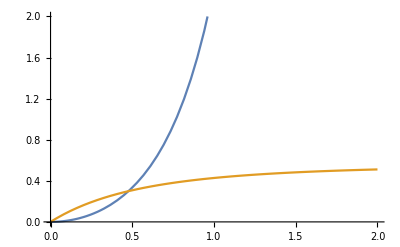

```mathematica
Plot[{λ Exp[λ^2]Erf[λ],λ Exp[λ^2]Erfc[λ]},{λ,0,2},PlotRange->{0,2}]
```

```mathematica
Subscript[T, ∞]
```

-3

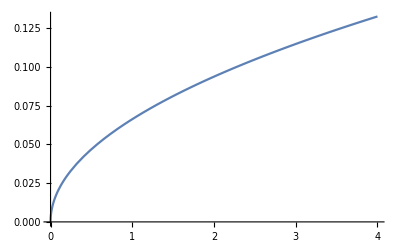

```mathematica
Plot[X[t]/.r,{t,0,4}]
```

```mathematica
T[x_,t_]:= Piecewise[{{Ts[x,t],X[t]>x},{Tl[x,t],x>X[t]}}]
```

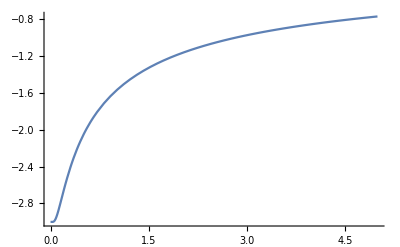

```mathematica
Plot[T[1,t]/.r,{t,0,5},PlotRange->All]
```

```mathematica
T[X[2],2]/.r
```

0

## Solidification of unit square

The analytical solution for semi-infinite domain involves the parameter λ which is determined by the physical properties of the material and boundary conditions. We fix boundary temperature to Tb at y = 0, and T0 is the initial (uniform) temperature of the liquid.  The parameter λ is given from the equation:
T_m-T_b=erf(λ)e^(λ^2)((λL √π)/C+ (T_0- T_m)/erfc(λ)e^(-λ^2))

Set the for the test calculations the λ, Tm and T0 and calculate Tb from this equation:

```mathematica
Clear[λ,L,c,Tl,Ts,Temp];
```

```mathematica
T0=1.2;c=1; L=1; Tm=1; λ=0.5;
```

```mathematica
Tb = Tm-Erf[λ] Exp[λ^2]((λ L √π)/c+((T0-Tm)Exp[-λ^2])/Erfc[λ]);
```

```mathematica
Tb
```

0.190602

Position of the interface is calculated using :

```mathematica
Y[t_]:= 2 λ √t;
```

The solid phase temperature is given :

```mathematica
Ts[y_,t_] := Tb + (Tm-Tb)/Erf[λ] Erf[η[y,t]];
```

```mathematica
η[y_,t_]:= y √(c/(4t));
```

And the liq. temperature profile:

```mathematica
Tl[y_,t_]:= T0+(Tm-T0)/Erfc[λ] Erfc[η[y,t]];
```

```mathematica
Temp[y_,t_]:=Piecewise[{{Ts[y,t],Y[t]> y},{Tl[y,t],y > Y[t]}}];
```

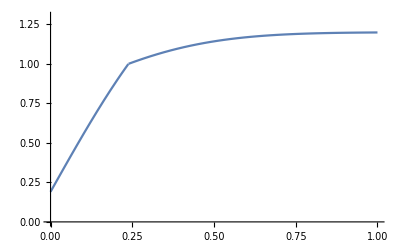

```mathematica
Plot[Temp[y,0.0568],{y,0,1},PlotRange->{0,1.3}]
```

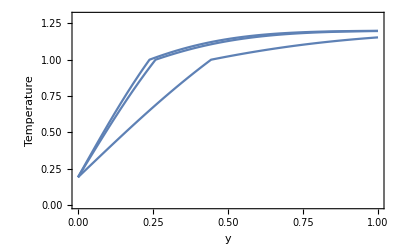

```mathematica
Plot[{Map[Temp[y,#]&,{0.0568,0.0668,0.1968}]},{y,0,1},PlotRange->{0,1.3},FrameLabel->{"y","Temperature"},Frame->True]
```

The position of the interface with melting temperature T = 1  is after 0.0568 s at position y = 0.2383

```mathematica
Y[0.0568]
```

0.238328

```mathematica
abaqData = Import["E:\\Dropbox\\Abaqus\\UMATHT\\Solidification\\8x8_mesh_temperature_profile_0_0586.txt","Table"];
```

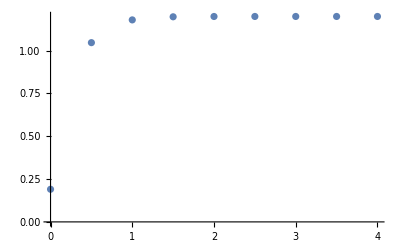

```mathematica
sh2=ListPlot[Drop[Drop[abaqData,3],-4],PlotRange->All]
```

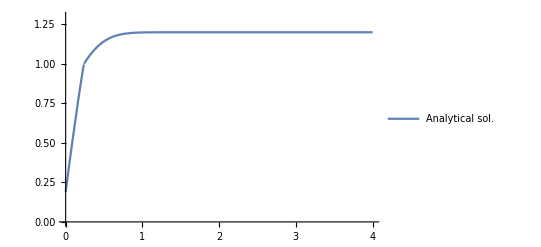

```mathematica
sh1=Plot[T[y,0.0568],{y,0,4},PlotRange->{0,1.3}, PlotLegends->{"Analytical sol."}]
```

Show::gcomb: Could not combine the graphics objects in ….

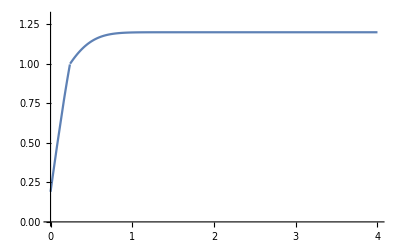
Show[{-Graphics-,-Graphics-,sh3},Frame→True,FrameLabel→{y,Temperature}]

```mathematica
Show[{sh1,sh2,sh3},Frame->True,FrameLabel->{"y","Temperature"}]
```

```mathematica
abaqFineData = Import["E:\\Dropbox\\Abaqus\\UMATHT\\Solidification\\Fine_mesh_temperature_profile_0_0586.txt","Table"];
```

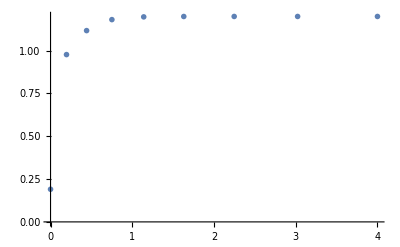

```mathematica
sh3=ListPlot[Drop[Drop[abaqFineData,3],-4],PlotRange->All,PlotMarkers->Red]
```

```mathematica
abaqDefaultData = Import["E:\\Dropbox\\Abaqus\\UMATHT\\Solidification\\Fine_mesh_temperature_profile_ABQ_default_0_0586.txt","Table"];
```

```mathematica
sh4=ListPlot[Drop[Drop[abaqDefaultData,2],-4],PlotRange->All,PlotMarkers->Pink,PlotLegends->{"ABQ default"}]
```

-Graphics-

```mathematica
abaqDefaultData
```

{{},{},{0.,0.1906},{0.19537,0.977246},{0.441243,1.11737},{0.750675,1.18156},{1.14009,1.19756},{1.63018,1.19981},{2.24695,1.19999},{3.02315,1.2},{4.,1.2},{},{},{},{}}

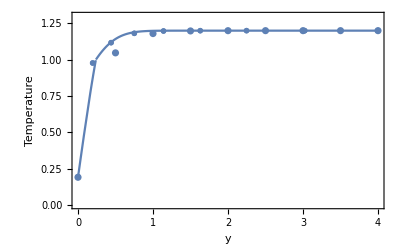

```mathematica
Show[{sh1,sh2,sh3,sh4},Frame->True,FrameLabel->{"y","Temperature"}]
```

```mathematica
abaqAppHeatData = Import["E:\\Dropbox\\Abaqus\\UMATHT\\Solidification\\Fine_mesh_temperature_profile_appHeat_0_0586.txt","Table"];
```

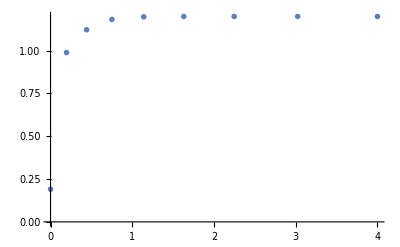

```mathematica
sh4=ListPlot[Drop[Drop[abaqAppHeatData,3],-4],PlotRange->All,PlotMarkers->Blue, PlotLegends->{"Apparent Heat"}]
```

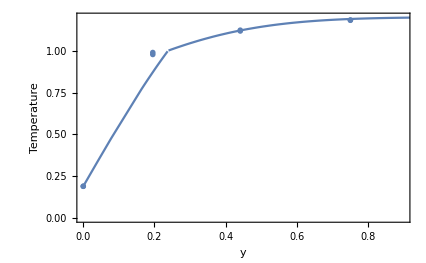

```mathematica
Show[{sh1,sh3,sh4},PlotRange->{{0,0.9},{0,1.2}},Frame->True,FrameLabel->{"y","Temperature"}]
```

```mathematica
abaqEntphlData = Import["E:\\Dropbox\\Abaqus\\UMATHT\\Solidification\\Fine_mesh_temperature_profile_Entphl_0_0586.txt","Table"];
```

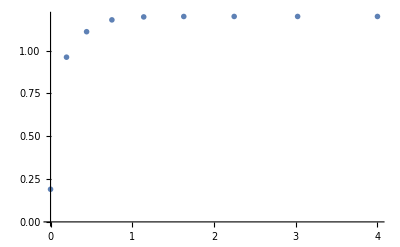

```mathematica
sh5=ListPlot[Drop[Drop[abaqEntphlData,3],-4],PlotRange->All,PlotMarkers->Blue,PlotLegends->{"Enthalpy"}]
```

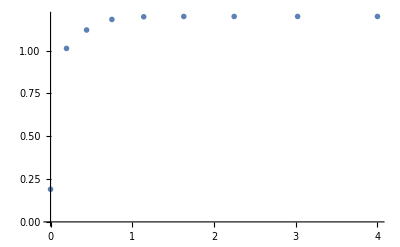

```mathematica
abaqEntphlGradData = Import["E:\\Dropbox\\Abaqus\\UMATHT\\Solidification\\Fine_mesh_temperature_profile_Enthalp_grad_0_0586.txt","Table"];
sh6=ListPlot[Drop[Drop[abaqEntphlGradData,3],-4],PlotRange->All,PlotMarkers->Green, PlotLegends->{"Enthalpy Grad"}]
```

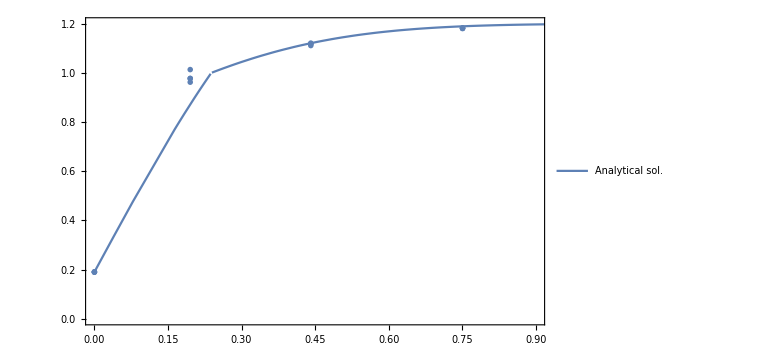

```mathematica
Show[{sh1,sh3,sh4,sh5,sh6},PlotRange->{{0,0.9},{0,1.2}},Frame->True,PlotLegends->{"y","Temperature"},ImageSize->Large]
```

```mathematica
Export["E:\\Dropbox\\My Writings\\Solidification\\Figs\\comparison_default_appHeat.pdf",%]
```

E:\Dropbox\My Writings\Solidification\Figs\comparison_default_appHeat.pdf

The error of the different approaches are calculated:

```mathematica
Total[Flatten[(abaqFineData-abaqEntphlData)]]
```

0.023278

```mathematica
analSol=T[#[[1]],0.0568]&/@Drop[Drop[abaqEntphlData,3],-4];
```

```mathematica
Total[Flatten[Abs[(Drop[Drop[abaqEntphlData,3],-4][[All,2]]-analSol)]/analSol]]
```

0.122438

```mathematica
Total[Flatten[Abs[(Drop[Drop[abaqFineData,3],-4][[All,2]]-analSol)]/analSol]]
```

0.132575

```mathematica
Total[Flatten[Abs[(Drop[Drop[abaqDefaultData,3],-4][[All,2]]-analSol)]/analSol]]
```

Thread::tdlen: Objects of unequal length in {0.977246,1.11737,1.18156,1.19756,1.19981,1.19999,1.2,1.2}+{-0.190602,-0.871479,-1.12055,-1.18918,-1.1997,-1.2,-1.2,-1.2,-1.2} cannot be combined.

12.2942 Abs[{0.977246,1.11737,1.18156,1.19756,1.19981,1.19999,1.2,1.2}+{-0.190602,-0.871479,-1.12055,-1.18918,-1.1997,-1.2,-1.2,-1.2,-1.2}]